```mathematica
Clear["Global`*"]
```

### Horizontal

#### 9in

{p→4.25287,wx→0.532451,a→4.28401}

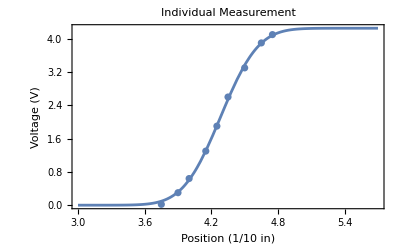

```mathematica
data=ImportString["4.75\t4.1
4.65\t3.9
4.5\t3.3
4.35\t2.6
4.25\t1.9
4.15\t1.3
4\t0.64
3.9\t0.3
3.75\t0.02
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
(*w0=.3;*)
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},PlotLabel->"Individual Measurement"],ListPlot[data],FrameLabel->{"Position (1/10 in)","Voltage (V)"},PlotRange->All,Frame->True]
```

#### 18in

{p→4.19948,wx→0.649947,a→4.21142}

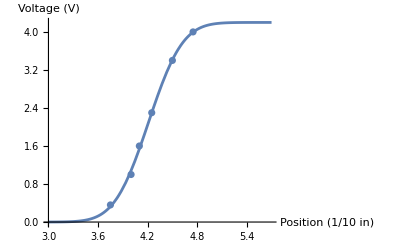

```mathematica
data=ImportString["4.75\t4
4.5\t3.4
4.25\t2.3
4.1\t1.6
4\t1
3.75\t0.36
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
```

#### 27in

{p→4.34868,wx→0.693407,a→4.33121}

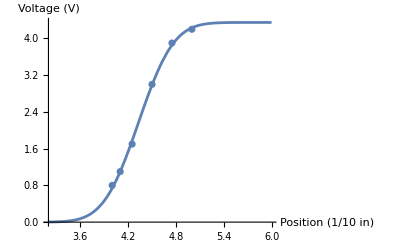

```mathematica
data=ImportString["5\t4.2
4.75\t3.9
4.5\t3
4.25\t1.7
4.1\t1.1
4\t0.8
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
```

### Vertical

#### 9in

{p→3.69923,wx→0.508404,a→0.629942}

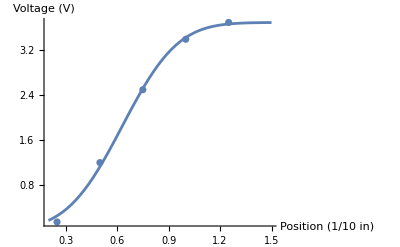

```mathematica
data=ImportString["1.25\t3.7
1\t3.4
0.75\t2.5
0.5\t1.2
0.25\t0.14
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
```

#### 18in

{p→3.6594,wx→0.542891,a→2.22829}

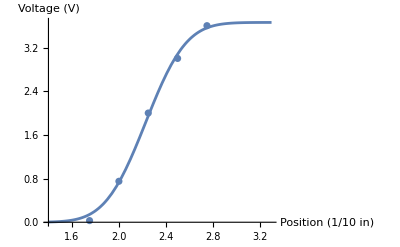

```mathematica
data=ImportString["2.75\t3.6
2.5\t3
2.25\t2
2\t0.75
1.75\t0.03
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
```

#### 27in

{p→3.77132,wx→0.643356,a→1.97389}

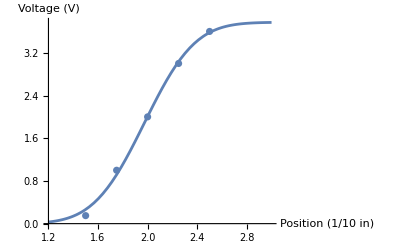

```mathematica
data=ImportString["2.5\t3.6
2.25\t3
2\t2
1.75\t1
1.5\t0.15
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
```

### Waist Size

#### Horizontal

{w0→0.00885803,d→50.6734}

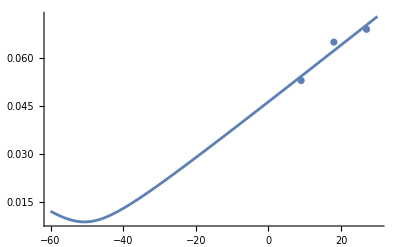

```mathematica
pos={9,18,27};
wx={.53,.65,.69}/10;
data1=Transpose@{pos,wx};
λ=2.5*10^-5;
w[z_]:=w0 Sqrt[(1+((z+d) λ/(Pi w0^2))^2)];
vars1=FindFit[data1,w[x],{{w0,.01},{d,50}},x,Method->NMinimize]
wfit1[x_]=w[x]/.vars1;
Show[Plot[wfit1[x],{x,-60,30}],ListPlot[data1],PlotRange->All]
wminx=vars1[[1,2]];
posminx=vars1[[2,2]];
```

```mathematica
wxlens=wfit1[260/25.4]*25.4(*waist size at lens placement*)
```

1.40796

```mathematica
wfit1[-43.5]*25.4(*waist size at laser*)
```

0.29288

#### Vertical

{w0→0.01081,d→57.0879}

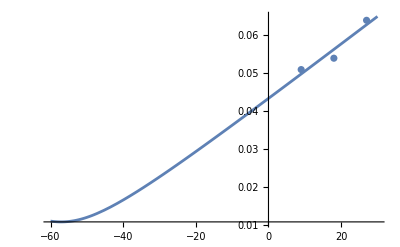

```mathematica
pos={9,18,27};
wx={.51,.54,.64}/10;
data2=Transpose@{pos,wx};
λ=2.5*10^-5;
w[z_]:=w0 Sqrt[(1+((z+d) λ/(Pi w0^2))^2)];
vars2=FindFit[data2,w[x],{{w0,.4},{d,-1}},x,Method->NMinimize]
wfit2[x_]=w[x]/.vars2;
Show[Plot[wfit2[x],{x,-60,30}],ListPlot[data2],PlotRange->All]
wminy=vars2[[1,2]];
posminy=vars2[[2,2]];
```

```mathematica
wylens=wfit2[260/25.4]*25.4(*waist size at lens placement*)
```

1.28844

```mathematica
wfit2[-43.5]*25.4(*waist size at laser*)
```

0.374088

```mathematica
Sqrt[wfit1[-43.5]^2+wfit1[-43.5]^2]*25.4
```

0.414194

### Both Plotted

```mathematica
Show[Plot[wfit2[x],{x,-60,30},PlotStyle->Orange,PlotLegends->{"Vertical"},PlotLabel->"Vertical and Horizontal Waist Measurements"],ListPlot[data2,PlotStyle->Orange,PlotLegends->{"Vertical"}],Plot[wfit1[x],{x,-60,30},PlotLegends->{"Horizontal"}],ListPlot[data1,PlotLegends->{"Horizontal"}],PlotRange->All,FrameLabel->{"Position (in)","Waist Size (in)"},Frame->True]
```

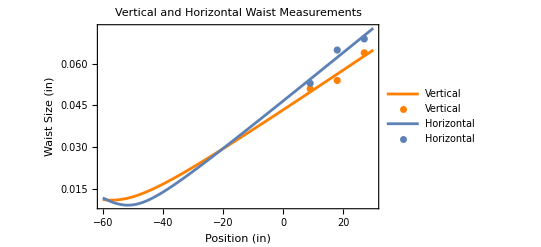

```mathematica
Sqrt[wminx^2+wminy^2]*25.4
```

```mathematica
0.35498250994996017
```

```mathematica
(posminx+posminy)/2*25.4
```

```mathematica
1368.568567003574
```

```mathematica
50*25.4
```

```mathematica
1270.
```

```mathematica
wminx*25.4
wminy*25.4
posminx*25.4
posminy*25.4
```

```mathematica
0.2249938704218523
```

```mathematica
0.27457301513981364
```

```mathematica
1287.1041271552228
```

```mathematica
1450.0330068519245
```

```mathematica
43.5*25.4
```

### Number 5

```mathematica
λ=635*10^-6;
inq[z_]:=1/(z+I*b);
M[iq_,A_]:=(A[[2,1]]+A[[2,2]]*iq)/(A[[1,1]]+A[[1,2]]*iq);
lensprop[f_,L_]:=({{1, L}, {0, 1}}).({{1, 0}, {-1/f, 1}});
Rad[iq_]:=1/Re[iq];
w[iq_]:=1/Sqrt[-Im[iq]*Pi/λ];
```

```mathematica
w0=Sqrt[wxlens^2+wylens^2];(*waist at location of lens placement in mm*)
b=Pi w0^2/λ;
iq=1/(260*(1+(b/260)^2))-I*λ/(Pi w0^2);
iqffunc[z_]:=M[iq,lensprop[100,z]];
wfunc[z_]:=w[iqffunc[z]];(*mm*)
Rfunc[z_]:=Rad[iqffunc[z]];
```

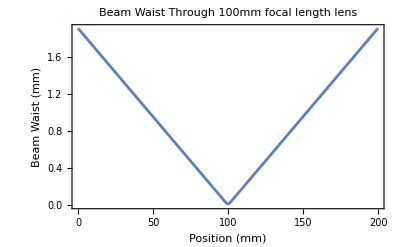

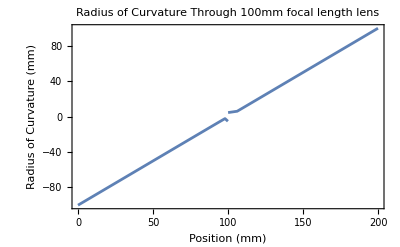

```mathematica
Plot[wfunc[z],{z,0,200},PlotLabel->"Beam Waist Through 100mm focal length lens",FrameLabel->{"Position (mm)","Beam Waist (mm)"},Frame->True]
Plot[Rfunc[z],{z,0,200},PlotLabel->"Radius of Curvature Through 100mm focal length lens",FrameLabel->{"Position (mm)","Radius of Curvature (mm)"},Frame->True]
```

```mathematica
FindMinimum[wfunc[z],{z,100}]
```

{0.0105915,{z→100.005}}

```mathematica
(*Equation 6 estimate*)
zm=100/(1+(100/b)^2)

(*Equation 7 estimate*)
w02=λ*100/(Pi w0)
```

99.9969

0.0105908

#### Minimum Beam Waist of Laser Placement

```mathematica
(*Placing lens at minimum waist*)
minw=Sqrt[wminx^2+wminy^2]*25.4

(*Equation 6 estimate*)
b=minw^2 Pi/λ;
zm=100/(1+(100/b)^2)

(*Equation 7 estimate*)
w02=λ*100/(Pi minw)
```

0.354983

97.4917

0.0569399

### 100mm Lens Waist Measurement

#### Horizontal

{p→4.14,wx→0.163161,a→4.25512}

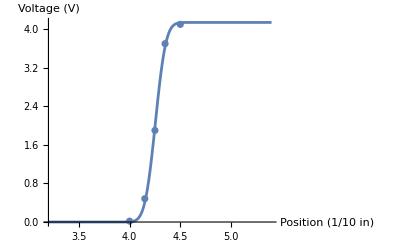

```mathematica
Clear[wx,w0];
data=ImportString["4.5\t4.1
4.35\t3.7
4.25\t1.9
4.15\t0.484
4\t0.018
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
minxlens=vars[[2,2]];
```

#### Vertical

{p→3.38837,wx→0.0990492,a→3.19173}

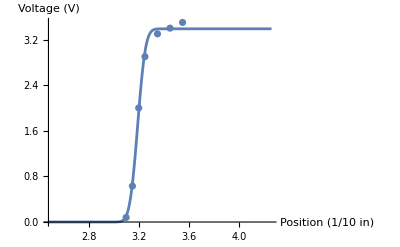

```mathematica
data=ImportString["3.55\t3.5
3.45\t3.4
3.35\t3.3
3.25\t2.9
3.2\t2
3.15\t0.63
3.1\t0.08
","TSV"];
P[x_]:=p/2(1+Erf[Sqrt[2]/wx (x-a)]);
Ptest[x_,p_,wx_]:=p/2(1+Erf[Sqrt[2]/wx x]);
p0=.108*2;
w0=.3;
vars=FindFit[data,P[x],{p,wx,a},x,Method->NMinimize]
Pfit[x_]=P[x]/.vars;
Show[Plot[Pfit[x],{x,Min[data[[All,1]]]-.2*Min[data[[All,1]]],Max[data[[All,1]]]+.2*Max[data[[All,1]]]},AxesLabel->{"Position (1/10 in)","Voltage (V)"}],ListPlot[data],PlotRange->All]
minylens=vars[[2,2]];
```

#### Comparison with 5

```mathematica
λ=635*10^-6;
inq[z_]:=1/(z+I*b);
M[iq_,A_]:=(A[[2,1]]+A[[2,2]]*iq)/(A[[1,1]]+A[[1,2]]*iq);
lensprop[f_,L_]:=({{1, L}, {0, 1}}).({{1, 0}, {-1/f, 1}});
Rad[iq_]:=1/Re[iq];
w[iq_]:=1/Sqrt[-Im[iq]*Pi/λ];

wminlens=Sqrt[minxlens^2+minylens^2]*2.54
Rcalc=-20*(1+(Pi wminlens^2/(λ *-20))^2)
w0=Sqrt[wxlens^2+wylens^2];
b=Pi w0^2/λ;
λ=635*10^-6;
iq=1/(340*(1+(b/340)^2))-I*λ/(Pi w0^2);
iqf=M[iq,lensprop[100,80]]
w[iqf]
Rad[iqf]
```

0.484816

-67632.9

-0.0499431-0.00138547 ⅈ

0.381956

-20.0228